```mathematica
Clear["Global`*"]
```

```mathematica
Solve[a v1+v2==a v1′+v2′&&a v1^2+v2^2==a v1′^2+v2′^2,{v1′,v2′}]//Simplify
```

{{v1′→v1,v2′→v2},{v1′→((-1+a) v1+2 v2)/(1+a),v2′→(2 a v1+v2-a v2)/(1+a)}}

```mathematica
P=1/(a+1)({{a-1, 2}, {2a, -a+1}});Q=({{1, 0}, {0, -1}});
S=Q.P//Simplify;
S//MatrixForm
```

((-1+a)/(1+a) | 2/(1+a)
-(2 a)/(1+a) | (-1+a)/(1+a))

```mathematica
l=Simplify[Eigenvalues[S],a>0]
𝒟=Simplify[Eigenvectors[S],a>0]
```

{(-ⅈ+√a)^2/(1+a),(ⅈ+√a)^2/(1+a)}

{{ⅈ/(√a),1},{-ⅈ/(√a),1}}

```mathematica
𝒟=Transpose[𝒟];
𝒟//MatrixForm
```

(ⅈ/(√a) | -ⅈ/(√a)
1 | 1)

```mathematica
2Inverse[𝒟]//MatrixForm
```

(-ⅈ √a | 1
ⅈ √a | 1)

```mathematica
vec=FullSimplify[MatrixPower[S,k].{-v0,0},a>0]//MatrixForm
```

(-1/2 (((-ⅈ+√a)^2/(1+a))^k+((ⅈ+√a)^2/(1+a))^k) v0
1/2 ⅈ √a (((-ⅈ+√a)^2/(1+a))^k-((ⅈ+√a)^2/(1+a))^k) v0)

```mathematica
vec1=FullSimplify[𝒟.DiagonalMatrix[l^k].Inverse[𝒟].{-v0,0}]//MatrixForm
vec-vec1//Simplify
```

(-1/2 (((-ⅈ+√a)^2/(1+a))^k+((ⅈ+√a)^2/(1+a))^k) v0
1/2 ⅈ √a (((-ⅈ+√a)^2/(1+a))^k-((ⅈ+√a)^2/(1+a))^k) v0)

0

```mathematica
λ=(-ⅈ+10^d)/(ⅈ+10^d);
vec2=Simplify[{10^d ⅈ(-λ^k+Conjugate[λ]^k),λ^k+Conjugate[λ]^k},d∈Reals]//MatrixForm
vec1-vec2//Simplify
```

(ⅈ 10^d (-((-ⅈ+10^d)/(ⅈ+10^d))^k+((ⅈ+10^d)/(-ⅈ+10^d))^k)
((-ⅈ+10^d)/(ⅈ+10^d))^k+((ⅈ+10^d)/(-ⅈ+10^d))^k)

0

0.199337

31

16

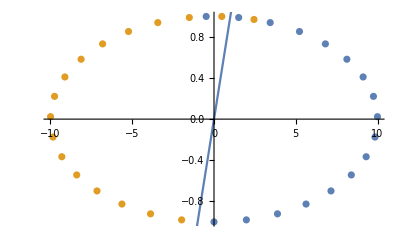

```mathematica
d=1;
θ=ArcTan[(-2*10^d)/(10^(2d)-1)];
θ′=Abs[θ];
N[θ′]
Floor[10^d*π]
k0=Floor[10^d*π/2]+1
list=Table[{10^d Sin[k θ′],-Cos[k θ′]},{k,0,k0}];
mA=1;mB=10^(2d);
P=1/(mA+mB)({{mA-mB, 2mB}, {2mA, -mA+mB}});
list2=Table[P.{10^d Sin[k θ′],-Cos[k θ′]},{k,0,k0}];
velo=ListPlot[{list,list2}];
line=Plot[x,{x,-10^d,10^d}];
Show[velo,line]
```

```mathematica
P.{10^d Sin[k θ′],-Cos[k θ′]}/.{k->1}
```

{-39600/10201,-9401/10201}